```mathematica
ClearAll;
```

```mathematica
ZZ1[x_]= x/(1-x^2)
ZZ2[x_]= x^2
ZZ3[x_]= (1/Pi)ArcTan[x] + 1/2
ZZ4[x_]= 1/x
```

x/(1-x^2)

x^2

1/2+ArcTan[x]/π

1/x

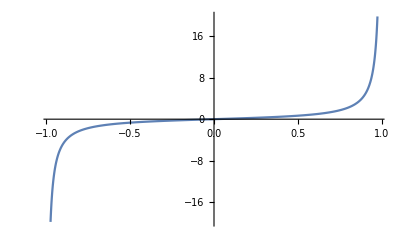

```mathematica
l1= 0.975;
Plot[ZZ1[x],{x,-l1,l1},PlotRange->Full]
```

```mathematica
l1= 100;
```

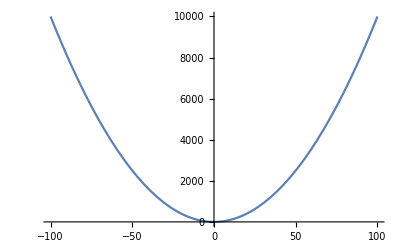

```mathematica
Plot[ZZ2[x],{x,-l1,l1}]
```

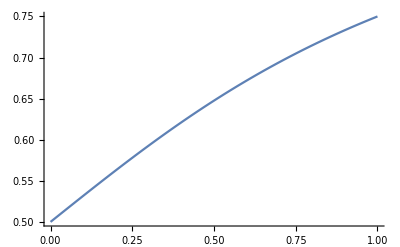

```mathematica
l1= 0.999999;
Plot[ZZ3[x],{x,0,l1},PlotRange->Full]
```

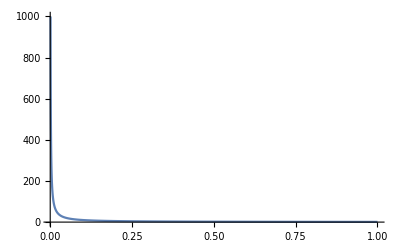

```mathematica
l1= 0.001;
l2 = 1;
Plot[ZZ4[x],{x,l1,l2},PlotRange->Full]
```

112 t-16 t^2

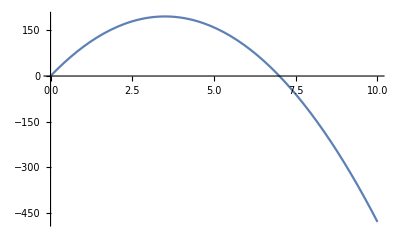

```mathematica
ZZ101[t_]= -16t^2 + 112t
Plot[ZZ101[t],{t,0,10}]
```